# MA2330

## 5.6 Summary

As a consequence of the diagonalization theorem.

Evals of A give the long time behavior of the Discrete Dynamical System x_(k+1)=A x_k

Complex evals a± b ⅈ are spirals in the re(v)—im(v) plane defined by evecs re(v)±im(v) ⅈ

real evals λ are stretches in the direction of the eigenvector.

## 5.7 Ordinary Differential Equations: x'=A x

The 2D linear ODE system x'=A x means 
	x_1' | = | a_11 x_1 | + | a_12 x_2
x_2' | = | a_21 x_1 | + | a_22 x_2
It should be clear what this means in high dimensions!  Solutions are functions that satisfy the equation!

The weighted sum z(t)=c_1 x(t)+c_2 y(t) of two solutions x(t) and y(t) is also a solution since 
	z'(t)=c_1 x'(t)+c_2 y'(t)=c_1(A x(t))+c_2(A y(t))=A (c_1 x(t)+c_2 y(t))=A z(t).

ODE texts show that there are always n linearly independent solutions of x'=A x in n dimensions.  A basis for the set of solutions is a  fundamental set of solutions. An Initial Value Problem (IVP) selects the unique solution satisfying x(t_0)=x_o.  A fundamental matrix Φ(t) has columns from a fundamental set of solutions. Note
	Φ'(t)=(y_1' | y_2' | … | y_n')=(A y_1 | A y_2 | … | A y_n)=A (y_1 | y_2 | … | y_n)=A Φ(t)  
Since the columns of Φ are a basis any solution x(t) has 
	x(t)=c_1 y_1(t)+…+c_n y_n(t)=Φ(t) (c_1
⋮
c_n)=Φ(t) c
and the solution to the IVP x(t_0)=x_0 is 
	 x(t)=Φ(t) c 
where the constants c are computed by solving Φ(t_0)c=x_0.

### Diagonalization: A=P D P^-1

If x'=A x then 
	x'=P D P^-1 x=P D (P^-1 x) ⟺ P^-1x'=P^-1 P D (P^-1 x)
and 
	(P^-1 x)'= D (P^-1 x) ⟺ y'=D y.
for diagonalizable matrices A the behavior of x'=A x is determined by the eigenvalues of A.

### Real Eigenvalues - (λ_1 | 0 0 | λ_2)

The system  
	(x_1
x_2)' | = | (λ_1 | 0
0 | λ_2) (x_1
x_2)
is simply 
	x_1' | =
x_2' | = | λ_1 x_1
λ_2 x_2
which has solutions 
	x_1 | =
x_2 | = | c_1 ⅇ^(λ_1 t)
c_2 ⅇ^(λ_2 t)
and a fundamental matrix is 
	Φ(t)=(ⅇ^(λ_1 t) | 0
0 | ⅇ^(λ_2 t)).

Both solutions grow if λ_1>0 and λ_2>0. “Repeller”

Both solutions decay to zero if λ_1<0 and λ_2<0. “Attractor”

One solution grows and the other decays if λ_1 λ_2<0. “Saddle”

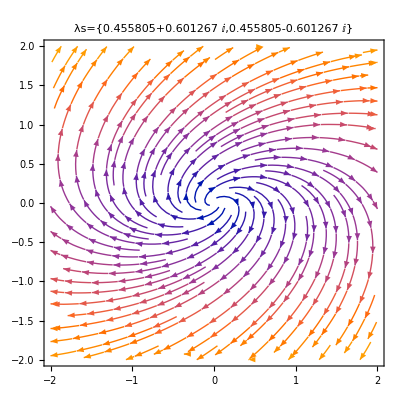

```mathematica
A=RandomReal[{-1,1},{2,2}];
StreamPlot[A.{x1,x2},{x1,-2,2},{x2,-2,2},
PlotLabel->StringForm["λs=``",Eigenvalues[A]]]
```

### Complex Eigenvalues λ=a ±b ⅈ

We have a choice of matrices (a | -b
b | a) or (a+ b ⅈ | 0
0 | a-b ⅈ).  The system
	(x_1
x_2)' | = | (a | -b
b | a) (x_1
x_2)
does not look much better when written out
	x_1' | =
x_2' | = | a x_1-b x_2
b x_1+a x_2
so we are stuck with trying to understand the complex diagonal system
	x_1' | =
x_2' | = | (a+b ⅈ) x_1
(a-b ⅈ) x_1
which has the “formal” solution
	x_1 | =
x_2 | = | c_1 ⅇ^((a+b ⅈ)t) | = | c_1∑_(k=0)^∞ (((a+b ⅈ)t)^k/k!)
c_2 ⅇ^((a-b ⅈ)t) | = | c_2∑_(k=0)^∞ (((a-b ⅈ)t)^k/k!)
because 
	e^z | =1+z+z^2/(2!)+z^3/(3!)+… | =∑_(k=0)^∞ (z^k/k!) 
The traditional way (in the book on p325-326) to get rid of the complex numbers is to work out that
	ⅇ^((a+b ⅈ)t)=ⅇ^(a t +b t ⅈ)=ⅇ^(a t+ b t ⅈ)=ⅇ^(a t) ⅇ^(b t ⅈ)=ⅇ^(a t) ∑_(k=1)^∞ (b t)^k ⅈ^k
you can split the sum up into even and odd terms
	ⅇ^((a+b ⅈ)t)=ⅇ^(a t)ⅇ^((b ⅈ)t)=ⅇ^(a t) ∑_(k=1)^∞ (b t)^k ⅈ^k=ⅇ^(a t) (∑_(j=0)^∞ (b t)^(2j)ⅈ^(2j)+∑_(j=0)^∞ (b t)^(2j+1)ⅈ^(2j+1))
and look for the pattern in the complex powers
	ⅈ^0 | = | 1
ⅈ^1 | = | ⅈ
ⅈ^2 | = | -1
ⅈ^3 | = | ⅈ
ⅈ^4 | = | □
ⅈ^5 | = | □
to get 
	ⅇ^((a+b ⅈ)t)=ⅇ^(a t) (∑_(j=0)^∞ (b t)^(2j)(-1)^j+ⅈ ∑_(j=0)^∞ (b t)^(2j+1)(-1)^j)
The last step is to recognize the series for cosine and sine to get
	ⅇ^((a+b ⅈ)t)=ⅇ^(a t) (cos(t)+i sin(t))
and naturally the conjugate version is 
	 ⅇ^((a-b ⅈ)t)=ⅇ^(a t) (cos(t)-i sin(t)).

```mathematica
MatrixExp[{{a,-b},{b,a}}]//MatrixForm
```

(ⅇ^a Cos[b] | -ⅇ^a Sin[b]
ⅇ^a Sin[b] | ⅇ^a Cos[b])

### Matrix Exponential: ⅇ^(A t) solves Φ'=A Φ

The series I+A t+A^2 t^2/(2!)+A^3 t^3/(3!)+… solves Φ'=A Φ since
	d/dt(I+A t+A^2 t^2/(2!)+A^3 t^3/(3!)+…)=(0+A +A^2(2 t^1)/(2!)+A^3(3 t^2)/(3!)+…)=A(I+A t+A^2 t^2/(2!)+…).
The matrix exponential is defined by the series 
	ⅇ^(A t)=I+A t+A^2 t^2/(2!)+A^3 t^3/(3!)+…=∑_(i=0)^∞ A^i t^i/(i!)

A direct computation gives
	ⅇ^((λ_1 | 0
0 | λ_2)t) | = | ∑_(i=0)^∞ (λ_1 | 0
0 | λ_2)^i t^i/(i!)=∑_(i=0)^∞ (λ_1^i | 0
0 | λ_2^i)t^i/(i!)=∑_(i=0)^∞ (λ_1^i t^i/(i!) | 0
0 | λ_2^i t^i/(i!))=(ⅇ^(λ_1 t) | 0
0 | ⅇ^(λ_2 t))

A fairly direct computation gives
	ⅇ^((a | -b
b | a)t) | = | ∑_(i=0)^∞ (a | -b
b | a)^i t^i/(i!)=∑_(i=0)^∞ (a/b | 0
0 | a/)^i(cos(θ) | -sin(θ)
sin(θ) | cos(θ))^i t^i/(i!)=∑_(i=0)^∞ (λ_1^i t^i/(i!) | 0
0 | λ_2^i t^i/(i!))=(ⅇ^(λ_1 t) | 0
0 | ⅇ^(λ_2 t))

```mathematica
A={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}};
Simplify[A.A.A.A.A.A.A]//MatrixForm
```

(Cos[7 θ] | -Sin[7 θ]
Sin[7 θ] | Cos[7 θ])

### Complex Eigenvalues λ=a ±b ⅈ

The system  
	(x_1
x_2)' | = | (λ_1 | 0
0 | λ_2) (x_1
x_2)
is simply 
	x_1' | =
x_2' | = | λ_1 x_1
λ_2 x_2
which has solutions 
	x_1 | =
x_2 | = | c_1 ⅇ^(λ_1 t)
c_2 ⅇ^(λ_2 t)
and a fundamental matrix is 
	Φ(t)=(ⅇ^(λ_1 t) | 0
0 | ⅇ^(λ_2 t)).

Both solutions grow if λ_1>0 and λ_2>0. “Repeller”

Both solutions decay to zero if λ_1<0 and λ_2<0. “Attractor”

One solution grows and the other decays is λ_1 λ_2<0. “Saddle”

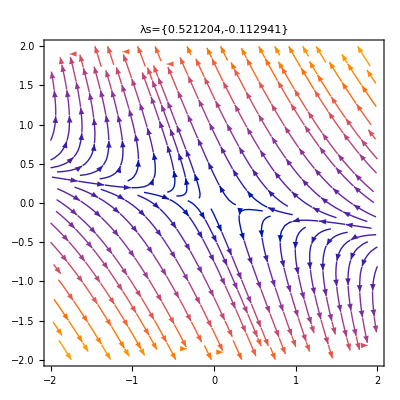

```mathematica
A=RandomReal[{-1,1},{2,2}];
StreamPlot[A.{x1,x2},{x1,-2,2},{x2,-2,2},
PlotLabel->StringForm["λs=``",Eigenvalues[A]]]
```

### Pictures of ODEs

It is pretty easy to plot solutions of Dynamical Systems in 2 or 3 dimensions.

#### 2D Pics

```mathematica
DySysPlot2D[A_]:= Module[
{x,Data, maxSteps=23,Δθ=π/11},
Data=Table[ 
x[0]={Cos[θ],Sin[θ]};
x[k_]:=A.x[k-1];
Table[x[k],{k,0,maxSteps}],
{θ,Δθ,2π,Δθ}];
ListPlot[Data,AspectRatio->Automatic,
Prolog->{Green, Circle[{0,0},1]},
Epilog->{Black,Arrowheads[Small],Thin,Map[Arrow,Data]},
PlotLabel->StringForm["λs = ``", NumberForm[Chop[Eigenvalues[A]],3]]]
]
```

```mathematica
A=({{0.9, 0.1}, {-0.104, 0.9}});
DySysPlot2D[A]
```

-Graphics-

Spiral if λ=a±b ⅈ.  Spins fast if |b/a|>1 is big.

Inwards if a^2+b^2<1.  Fast if a^2+b^2 is near zero.

Outwards if a^2+b^2>1. Fast if a^2+b^2 is big

Attractor, Repeller, or Saddle if λ_1 and λ_2 are real

Attractor if |λ_1|<1 and |λ_2|<1

Repeller if |λ_1| > 1 and |λ_2| > 1

Saddle if |λ_1| > 1 and |λ_2| < 1 (or the other way around)

```mathematica
A=({{0.5, 0.4}, {-0.104, 1.1}});
DySysPlot2D[A]
```

-Graphics-

#### 3D Pics

```mathematica
DySysPlot3D[A_]:= Module[
{x,Data, maxSteps=23,Δθ=π/6},
Data=Flatten[Table[ 
x[0]={Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]};
x[k_]:=A.x[k-1];
Table[x[k],{k,0,maxSteps}],
{ϕ,Δθ,π-Δθ,Δθ},{θ,Δθ,2π,Δθ}],1];
Show[
Graphics3D[{Opacity[0.2],LightGreen,Sphere[{0,0,0},1]}],
ListLinePlot3D[Data,BoxRatios->Automatic,
PlotMarkers->{"Point",Small},
PlotStyle->Thin],
PlotLabel->StringForm["λs = ``", NumberForm[Chop[Eigenvalues[A]],3]],
Axes->True
]]
```

Your book does not make up names for all of the cases in 3D.

```mathematica
A=({{0.9, 0.1, 0}, {-0.1, 0.9, 0}, {0, 0, 0.5}});
DySysPlot3D[A]
```

-Graphics3D-

```mathematica
A=({{1.05, 0, 0}, {0, 0.6, 0}, {0, 0, 0.5}});
DySysPlot3D[A]
```

-Graphics3D-

## Summary

As a consequence of the diagonalization theorem.

Evals of A give the long time behavior of the Discrete Dynamical System x_(k+1)=A x_k

Complex evals a± b ⅈ are spirals in the re(v)—im(v) plane defined by evecs re(v)±im(v) ⅈ

real evals λ are stretches in the direction of the eigenvector.

## Row Op Code

```mathematica
Clear[RowScale,RowSwitch,RowAdd]
RowScale[A_,{i_, α_}]:=Module[{ANew=A,s},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
ANew⟦i,All⟧=α ANew⟦i,All⟧;
s⟦i⟧=StringForm["row_(``)→(``)row_(``)",i,α,i];
Print[MatrixForm[ANew],TableForm[s]];
ANew]
RowSwitch[A_,{i_,j_}]:=Module[{ANew=A,s},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
s⟦i⟧=StringForm["row_(``)→row_(``)",i,j];
s⟦j⟧=StringForm["row_(``)→row_(``)",j,i];
ANew⟦{i,j},All⟧=ANew⟦{j,i},All⟧;
Print[MatrixForm[ANew],TableForm[s]];
ANew]
RowAdd[A_,{i_,α_,p_}]:=Module[{ANew=A,s},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
s⟦i⟧=StringForm["row_(``)→ row_(``)+((``row)_(``))",i,i,α, p];
ANew⟦i,All⟧=ANew⟦i,All⟧+ α ANew⟦p,All⟧;
Print[MatrixForm[ANew],TableForm[s]];
ANew]
Clear[RowAdd]
RowAdd[A_,{iαs_,p_}]:=Module[{ANew=A,s,i,α},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
Do[
{i,α}=iαs⟦j⟧;
s⟦i⟧=StringForm["row_(``)→ row_(``)+((``row)_(``))",i,i,α, p];
ANew⟦i,All⟧=ANew⟦i,All⟧+ α ANew⟦p,All⟧,
{j,Length[iαs]}];
ANew=Simplify[ANew];
Print[MatrixForm[ANew],TableForm[s]];
ANew]
```